# Ejemplo 2 Manivela - Corredera

## Funciones

```mathematica
(*Matrices de Rotación*)
Rx[γ_]:=({{1, 0, 0}, {0, Cos[γ], -Sin[γ]}, {0, Sin[γ], Cos[γ]}});
Ry[β_]:=({{Cos[β], 0, Sin[β]}, {0, 1, 0}, {-Sin[β], 0, Cos[β]}});
Rz[α_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}});

MatrixForm[Rx[A]]
MatrixForm[Ry[A]]
MatrixForm[Rz[A]]
```

(1 | 0 | 0
0 | Cos[A] | -Sin[A]
0 | Sin[A] | Cos[A])

(Cos[A] | 0 | Sin[A]
0 | 1 | 0
-Sin[A] | 0 | Cos[A])

(Cos[A] | -Sin[A] | 0
Sin[A] | Cos[A] | 0
0 | 0 | 1)

## Datos

```mathematica
x21=0.15;(*m*)
y43=0.15;
x87=0.6;
y98=0.04;
x1110=0.3;
y1211=0.04;
x1413=0.25;
z1615=0.9;
z1918=0.25;

β10=330*Degree;
β1716=180*Degree;
β1817=90*Degree;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
(*-----------------------------Posicion-----------------------------*)
I3x3 = IdentityMatrix[3];

in={1,0,0};
jn={0,1,0};
kn={0,0,1};
I0=in;
J0=jn;
K0=kn;
(*_______________Matrices de rotación____________*)
(*Junta rotacional*)
C01=Ry[β10];(*Rotación sobre y/j*)
C02=Ry[β10];(*Paralelo al anterior*)
C03=Ry[β10].Rx[θ32];(*Rotación sobre x/i*)
C04=Ry[β10].Rx[θ32];(*Paralelo al anterior*)
(*Junta Esférica*)
C05=Ry[β10].Rx[θ32].Rx[θ54];(*Rotación sobre x/i*)
C06=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65];(*Rotación sobre y/j*)
C07=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76];(*Rotación sobre z/k*)
(*Junta rotacional 2*)
C08=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76];(*Paralelo al anterior*)
C09=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76];(*Paralelo al anterior*)
C010=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109];(*Rotación sobre y/j*)
(*Junta Rotacional 3*)
C011=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109];(*Paralelo al anterior*)
C012=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109];(*Paralelo al anterior*)
C013=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312];(*Rotación sobre y/j*)
(*Junta Rotacional 4*)
C014=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312];(*Paralelo al anterior*)
C015=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312].Rx[θ1514];(*Rotación sobre x/i*)
C016=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312].Rx[θ1514];(*Paralelo al anterior*)
C017=C016.Rz[β1716];(*Rotación sobre z/k*)
C018=C017.Ry[β1817];(*Rotación sobre y/j*)
C019=C018;(*Paralelo al anterior*)

(*__________Dirección de los vectores__________*)
(*Posición*)
I1=C01.in;
J3=C03.jn;
I7=C07.in;
J8=C08.jn;
I10=C010.in;
J11=C011.jn;
I13=C013.in;
K15=C015.kn;
K18=C018.kn;
(*Velocidad*)
I2=C02.in;
I4=C04.in;
J5=C05.jn;
K6=C06.kn;
J9=C09.jn;
J12=C012.jn;(*Rotación y*)
I14=C014.in;(*Rotación x*)

(*__________Velocidades angulares__________*)
ω32=dθ32*I2;(*Rotación x*)
ω54=dθ54*I4;(*Rotación x*)
ω65=dθ65*J5;(*Rotación y*)
ω76=dθ76*K6;(*Rotación z*)
ω109=dθ109*J9;(*Rotación y*)
ω1312=dθ1312*J12;(*Rotación y*)
ω1514=dθ1514*I14;(*Rotación x*)

ω3=ω32;
ω7=ω32+ω54+ω65+ω76;
ω8=ω7;(*????*)
ω10=ω32+ω54+ω65+ω76+ω109;
ω11=ω32+ω54+ω65+ω76+ω109+ω1312;

(*__________Aceleraciones angulares__________*)

α32=ddθ32*I2;
α54=ddθ54*I4+ω32×ω54;
α65=ddθ65*J5+(ω32+ω54)×ω65;
α76=ddθ76*K6+(ω32+ω54+ω65)×ω76;
α109=ddθ109*J9+(ω32+ω54+ω65+ω76)×ω109;
α1312=ddθ1312*J12+(ω32+ω54+ω65+ω76+ω109)×ω1312;
α1514=ddθ1514*I14+(ω32+ω54+ω65+ω76+ω109+ω1312)×ω1514;

α3=α32;
α7=α32+α54+α65+α76;
α8=α7;(*????*)
α10=α32+α54+α65+α76+α109;
α11=α32+α54+α65+α76+α109+α1312;

(*__________Definición de vectores__________*)
(*Posición*)
P21=x21*I1;
P43=y43*J3;
P87=x87*I7;
P98=y98*J8;
P1110=x1110*I10;
P1211=-y1211*J11;
P1413=x1413*I13;
P1615=z1615*K15;
P1918=z1918*K18;
(*Velocidad*)
V21={0,0,0};(*No cambia de dirección ni magnitud*)
V43=ω3×P43;(*Cambia solo de dirección*)
V87=ω7×P87;(*Cambia solo de dirección*)
V98=ω8×P98;(*Cambia solo de dirección*)
V1110=ω10×P1110;(*Cambia solo de dirección*)
V1211=ω11×P1211;(*Cambia solo de dirección*)
V1413={0,0,0};(*No cambia de dirección ni magnitud*)
V1615={0,0,0};(*No cambia de dirección ni magnitud*)
V1918={0,0,0};(*No cambia de dirección ni magnitud*)
(*Aceleración*)
A21={0,0,0};(*No cambia de dirección ni magnitud*)
A43=α3×P43+ω3×(ω3×P43);(*Cambia solo de dirección*)
A87=α7×P87+ω7×(ω7×P87);(*Cambia solo de dirección*)
A98=α8×P98+ω8×(ω8×P98);(*Cambia solo de dirección*)
A1110=α10×P1110+ω10×(ω10×P1110);(*Cambia solo de dirección*)
A1211=α11×P1211+ω11×(ω11×P1211);(*Cambia solo de dirección*)
A1413={0,0,0};(*No cambia de dirección ni magnitud*)
A1615={0,0,0};(*No cambia de dirección ni magnitud*)
A1918={0,0,0};(*No cambia de dirección ni magnitud*)

(*-----------------------------Ecuaciones de Posición-----------------------------*)
Pos1 = P21+P43+P87+P98+P1110+P1211+P1413+P1615+P1918;
Pos2 =C019-I3x3;
(*-----------------------------Ecuaciones de Velocidad-----------------------------*)

(*FO = Funcion objetivo*)
FO = ∑_(i=1)^3 Pos1[[i]]^2+∑_(j=1)^3 ∑_(k=1)^3 Pos2[[j,k]]^2;

Vel1 = V21+V43+V87+V98+V1110+V1211+V1413+V1615+V1918;
Vel2=ω32+ω54+ω65+ω76+ω109+ω1312+ω1514;

Acel1 = A21+A43+A87+A98+A1110+A1211+A1413+A1615+A1918;
Acel2=α32+α54+α65+α76+α109+α1312+α1514;


MatrixForm[Pos1]
```

(0.129904-0.075 Sin[θ32]+0.6 (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76])+0.3 (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+0.25 (Cos[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))-Sin[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.25 (-Cos[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.9 (-Sin[θ1514] (Cos[θ76] (-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54])-(1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])+Cos[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))))
0.+0.15 Cos[θ32]+0.6 (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76])+0.3 (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+0.25 (Cos[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))-Sin[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76])))+0.25 (-Cos[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76])))+0.9 (-Sin[θ1514] (Cos[θ76] (Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54])+(-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65] Sin[θ76])+Cos[θ1514] (Sin[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))))
0.075+0.129904 Sin[θ32]+0.6 (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])+0.3 (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+0.25 (Cos[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))-Sin[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.25 (-Cos[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.9 (-Sin[θ1514] (Cos[θ76] (1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54])-(Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])+Cos[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))))

## Solución de la Posición

### Solución inicial

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree;
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
PosInicial=FindMinimum[FO,
{
{θ54,Random[]},
{θ65,Random[]},
{θ76,Random[]},
{θ109,61*Degree},
{θ1312,42*Degree},
{θ1514,168*Degree}
}, MaxIterations ->25]
(*FindMinimum entrega un valor residual*)

{θ32,θ54,θ65,θ76,θ109,θ1312,θ1514}/Degree/.PosInicial[[2]]
```

{7.49504×10^-31,{θ54→-0.0485152,θ65→0.281497,θ76→-0.173222,θ109→1.07529,θ1312→0.741662,θ1514→2.94922}}

{0,-2.77972,16.1286,-9.92491,61.6093,42.4941,168.978}

### Dibujo:Solución inicial

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree;
Pos1 = P21+P43+P87+P98+P1110+P1211+P1413+P1615+P1918;
P0={0,0,0};
P1=P21;
P2=P21+P43;
P3=P21+P43+P87;
P4=P21+P43+P87+P98;
P5=P21+P43+P87+P98+P1110;
P6=P21+P43+P87+P98+P1110+P1211;
P7=P21+P43+P87+P98+P1110+P1211+P1413;
(*Manivela*)
Manivela=Tube[{P0,P1,P2},0.006]/.PosInicial[[2]];
ManEsf=Sphere[P2,0.01]/.PosInicial[[2]];(*Junta esférica*)
(*Barra1*)
Ba1Esf=Sphere[P2,0.015]/.PosInicial[[2]];(*Junta esférica*)
Barra1 = Tube[{P2,P3},0.007]/.PosInicial[[2]];(*Cuerpo Barra 1*)
CilBar1 = Cylinder[{P3,P4},0.009]/.PosInicial[[2]];
(*Barra2*)
Barra2 = Tube[{P4,P5},0.006]/.PosInicial[[2]];(*Cuerpo Barra 2*)
(*Barra3*)
Barra3 = Tube[{P6,P7},0.006]/.PosInicial[[2]];(*Cuerpo Barra 3*)
(*Base*)
Pmin1={-0.12,0.15,-0.25};
Pmax1={1,-0.15,-0.27};
Cubo1=Cuboid[Pmin1,Pmax1];
(*Cara 1 Prisma 1*)
a1={-0.039,-0.1,-0.2};
b1={0.071,-0.1,-0.2};
c1={-0.039,-0.1,0.1};

(*Cara 2 Prisma 1*)
a2={-0.039,0.1,-0.2};
b2={0.071,0.1,-0.2};
c2={-0.039,0.1,0.1};
Prisma1=Prism[{a1,b1,c1,a2,b2,c2}];
Cuerpo1=Graphics3D[{GrayLevel[0.913725],Cubo1,Prisma1}];(*Base*)
Cuerpo2=Graphics3D[{RGBColor[0,1,0],Manivela,ManEsf}];(*Manivela*)
Cuerpo3=Graphics3D[{RGBColor[1,0,0],Ba1Esf,Barra1,CilBar1}];(*Barra1*)
Cuerpo4=Graphics3D[{RGBColor[0,0,1],Barra2}];(*Barra2*)
Cuerpo5=Graphics3D[{RGBColor[0,1,1],Barra3}];(*Barra3*)
Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,Cuerpo5,
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,1,0}]
```

-Graphics3D-

### Solución Total

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree

θ54i=θ54/.PosInicial[[2]];
θ65i=θ65/.PosInicial[[2]];
θ76i=θ76/.PosInicial[[2]];
θ109i=θ109/.PosInicial[[2]];
θ1312i=θ1312/.PosInicial[[2]];
θ1514i=θ1514/.PosInicial[[2]];

For[i=0, i<=360, i+=1,
θ32=i*Degree;
SolPos[i]=FindMinimum[FO,
{
{θ54,θ54i},
{θ65,θ65i},
{θ76,θ76i},
{θ109,θ109i},
{θ1312,θ1312i},
{θ1514,θ1514i}
}, MaxIterations ->15];
θ54i=θ54/.SolPos[i][[2]];
θ65i=θ65/.SolPos[i][[2]];
θ76i=θ76/.SolPos[i][[2]];
θ109i=θ109/.SolPos[i][[2]];
θ1312i=θ1312/.SolPos[i][[2]];
θ1514i=θ1514/.SolPos[i][[2]];
];
SolPos[0]
```

0

{7.49504×10^-31,{θ54→-0.0485152,θ65→0.281497,θ76→-0.173222,θ109→1.07529,θ1312→0.741662,θ1514→2.94922}}

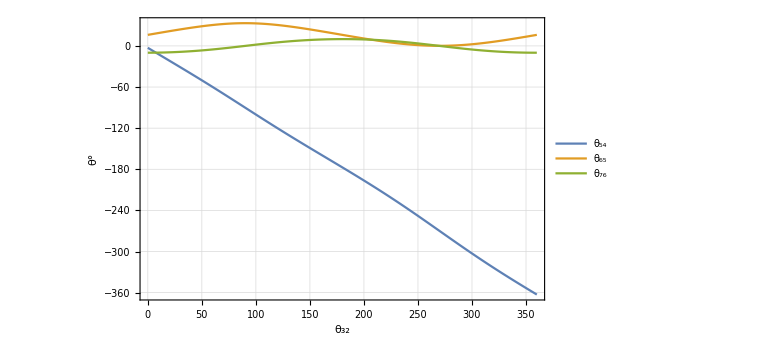

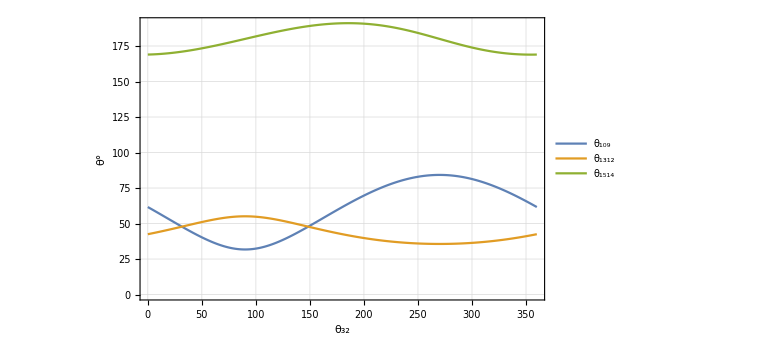

```mathematica
PTable1 = Table[{i,θ54/Degree}/.SolPos[i][[2]],{i,0,360,1}];(*Tabla 1 posición*)
PTable2 = Table[{i,θ65/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable3 = Table[{i,θ76/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable4 = Table[{i,θ109/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable5 = Table[{i,θ1312/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable6 = Table[{i,θ1514/Degree}/.SolPos[i][[2]],{i,0,360,1}];
TablaAngulos = {PTable1,PTable2,PTable3};
TablaAngulos2 = {PTable4,PTable5,PTable6};
ListLinePlot[TablaAngulos,PlotLegends->{"θ_54", "θ_65","θ_76"},
Frame->True,FrameLabel->{"θ_32", "θ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[TablaAngulos2,PlotLegends->{"θ_109","θ_1312","θ_1514"},
Frame->True,FrameLabel->{"θ_32", "θ°"},GridLines->Automatic, ImageSize->Large
]
```